{{:0,:1,:2},{3.,0,0},{2.9,0,0},{2.8,0,0},{2.7,0,0},{2.6,0,0},{2.5,0,0},{2.4,0,0},{2.3,0,0},{2.2,0,0},{2.1,0,0},{2.,0,0},{1.9,0,0},{1.8,0,0},{1.7,0,0},{1.6,0,0},{1.5,0,0},{1.4,0,0},{1.3,0,0},{1.2,0,0},{1.1,0,0},{1.,0,0}}

{{3.,0,0},{2.9,0,0},{2.8,0,0},{2.7,0,0},{2.6,0,0},{2.5,0,0},{2.4,0,0},{2.3,0,0},{2.2,0,0},{2.1,0,0},{2.,0,0},{1.9,0,0},{1.8,0,0},{1.7,0,0},{1.6,0,0},{1.5,0,0},{1.4,0,0},{1.3,0,0},{1.2,0,0},{1.1,0,0},{1.,0,0}}

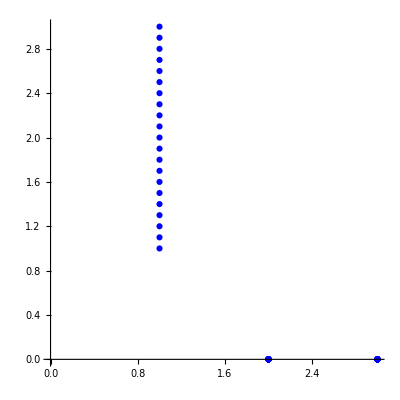

21

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/1d/line/solution/vertices.csv"]
tabve=Table[tabve[[i]],{i,2,Length[tabve]}]
ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
Length[tabve]
```

```mathematica
(*write ψ from ODE to csv file*)
```

```mathematica
tabψ=Table[{ψ[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabψ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{2.5,3.,0,0},{2.30665,2.9,0,0},{2.08133,2.8,0,0},{1.8293,2.7,0,0},{1.55778,2.6,0,0},{1.2757,2.5,0,0},{0.992908,2.4,0,0},{0.719046,2.3,0,0},{0.462526,2.2,0,0},{0.229794,2.1,0,0},{0.0250805,2.,0,0},{-0.149426,1.9,0,0},{-0.293168,1.8,0,0},{-0.406739,1.7,0,0},{-0.491451,1.6,0,0},{-0.54902,1.5,0,0},{-0.581361,1.4,0,0},{-0.590486,1.3,0,0},{-0.578483,1.2,0,0},{-0.547539,1.1,0,0},{-0.5,1.,0,0}}

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution_ode/psi_ode.csv",tabψ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution_ode/psi_ode.csv

```mathematica
(*write μ from ODE to csv file*)
```

```mathematica
tabμ=Table[{H[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabμ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{-1.06733,3.,0,0},{-1.28394,2.9,0,0},{-1.47877,2.8,0,0},{-1.63912,2.7,0,0},{-1.75213,2.6,0,0},{-1.80788,2.5,0,0},{-1.80216,2.4,0,0},{-1.73769,2.3,0,0},{-1.62325,2.2,0,0},{-1.47114,2.1,0,0},{-1.29424,2.,0,0},{-1.10384,1.9,0,0},{-0.90848,1.8,0,0},{-0.713843,1.7,0,0},{-0.5232,1.6,0,0},{-0.338073,1.5,0,0},{-0.158896,1.4,0,0},{0.0144215,1.3,0,0},{0.182076,1.2,0,0},{0.344065,1.1,0,0},{0.5,1.,0,0}}

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution_ode/mu_ode.csv",tabμ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution_ode/psi_ode.csv